```mathematica
((p v[r[s]])/r[s])^2==FullSimplify[1-1/({r[s]Cos[θ[s]],r[s]Sin[θ[s]]}.{r[s]Cos[θ[s]],r[s]Sin[θ[s]]}D[{r[s]Cos[θ[s]],r[s]Sin[θ[s]]},s].D[{r[s]Cos[θ[s]],r[s]Sin[θ[s]]},s])({r[s]Cos[θ[s]],r[s]Sin[θ[s]]}.D[{r[s]Cos[θ[s]],r[s]Sin[θ[s]]},s])^2]
```

(p^2 v[r[s]]^2)/r[s]^2==(r[s]^2 θ'[s]^2)/(r'[s]^2+r[s]^2 θ'[s]^2)

```mathematica
(p v[r[s]]^2)/r[s]^2== θ'[s]
r'[s]^2+r[s]^2 θ'[s]^2==v[r[s]]^2
```

(p v[r[s]]^2)/r[s]^2==θ'[s]

r'[s]^2+r[s]^2 θ'[s]^2==v[r[s]]^2

```mathematica
(r'[s]r[s])/Sqrt[v[r[s]]^2 r[s]^2-p^2 v[r[s]]^4]==1
```

(r[s] r'[s])/(√(r[s]^2 v[r[s]]^2-p^2 v[r[s]]^4))==1

```mathematica
v[r_]:=v0(r0/r)^α
```

```mathematica
Integrate[r/Sqrt[v[r]^2 r^2-p^2 v[r]^4],r]
```

```mathematica
Solve[Log[r]/(√(1-p^2))==s+c1,r]
```

{{r→ConditionalExpression[ⅇ^(√(1-p^2) (c1+s)),-π<Im[√(1-p^2) (c1+s)]≤π]}}

```mathematica
r[s_]:=ⅇ^(√(1-p^2) (c1+s))
```

```mathematica
DSolve[(p v[r[s]]^2)/r[s]^2==θ'[s],θ[s],s]
```

{{θ[s]→p s+C[1]}}

```mathematica
θ[s_]:=p s+c2
```

```mathematica
p=1;
c1=0;
c2=0;
```

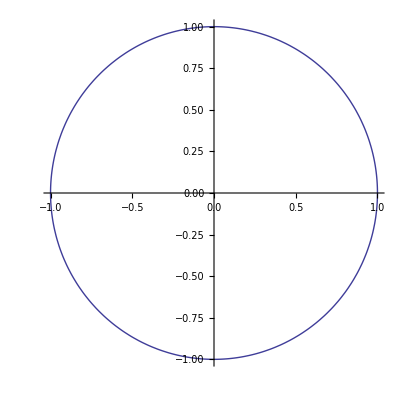

```mathematica
ParametricPlot[{r[s]Cos[θ[s]],r[s]Sin[θ[s]]},{s,-π,π},AspectRatio->1]
```

```mathematica
((p v[r[s]])/r[s])^2==
```

```mathematica
α=1
```

1

```mathematica
Integrate[r/Sqrt[v[r]^2 r^2-p^2 v[r]^4],r]
```

(r^2 √(r0^2 v0^2-(p^2 r0^4 v0^4)/r^4))/(2 r0^2 v0^2)

```mathematica
Clear[α]
```

```mathematica
α=5;
FullSimplify[Integrate[r/Sqrt[v[r]^2 r^2-p^2 v[r]^4],r]-(r^(2α) √((r0^(2α) v0^2 (r^(2α+2)-p^2 r0^(2α) v0^2))/r^(4α)))/((α+1) r0^(2α) v0^2)]
```

0

```mathematica
FullSimplify[(r^(2α) √((r0^(2α) v0^2 (r^(2α+2)-p^2 r0^(2α) v0^2))/r^(4α)))/((α+1) r0^(2α) v0^2)]
```

(r^(2 α) r0^(-2 α) √(r^(-4 α) r0^(2 α) v0^2 (r^(2+2 α)-p^2 r0^(2 α) v0^2)))/(v0^2 (1+α))

```mathematica
α=1
```

1

```mathematica
Solve[(r^(2 α) r0^(-2 α) √(r^(-4 α) r0^(2 α) v0^2 (r^(2+2 α)-p^2 r0^(2 α) v0^2)))/(v0^2 (1+α))==s+c1,r]
```

```mathematica
α=4;
Solve[(r^(2 α) r0^(-2 α) √(r^(-4 α) r0^(2 α) v0^2 (r^(2+2 α)-p^2 r0^(2 α) v0^2)))/(v0^2 (1+α))==c1+s,r]
```

{{r→-r0^(4/5) (25 c1^2+p^2+50 c1 s+25 s^2)^(1/10) v0^(1/5)},{r→r0^(4/5) (25 c1^2+p^2+50 c1 s+25 s^2)^(1/10) v0^(1/5)},{r→-(-1)^(1/5) r0^(4/5) (25 c1^2+p^2+50 c1 s+25 s^2)^(1/10) v0^(1/5)},{r→(-1)^(1/5) r0^(4/5) (25 c1^2+p^2+50 c1 s+25 s^2)^(1/10) v0^(1/5)},{r→-(-1)^(2/5) r0^(4/5) (25 c1^2+p^2+50 c1 s+25 s^2)^(1/10) v0^(1/5)},{r→(-1)^(2/5) r0^(4/5) (25 c1^2+p^2+50 c1 s+25 s^2)^(1/10) v0^(1/5)},{r→-(-1)^(3/5) r0^(4/5) (25 c1^2+p^2+50 c1 s+25 s^2)^(1/10) v0^(1/5)},{r→(-1)^(3/5) r0^(4/5) (25 c1^2+p^2+50 c1 s+25 s^2)^(1/10) v0^(1/5)},{r→-(-1)^(4/5) r0^(4/5) (25 c1^2+p^2+50 c1 s+25 s^2)^(1/10) v0^(1/5)},{r→(-1)^(4/5) r0^(4/5) (25 c1^2+p^2+50 c1 s+25 s^2)^(1/10) v0^(1/5)}}

```mathematica
r0^(α/(α+1)) ((α+1)^2 c1^2+p^2+2(α+1)^2 c1 s+(α+1)^2 s^2)^(1/(2(α+1))) v0^(1/(α+1))-r0^(4/5) (25 c1^2+p^2+50 c1 s+25 s^2)^(1/10) v0^(1/5)
```

0

```mathematica
FullSimplify[r0^(α/(α+1)) ((α+1)^2 c1^2+p^2+2(α+1)^2 c1 s+(α+1)^2 s^2)^(1/(2(α+1))) v0^(1/(α+1))]
```

```mathematica
r[s_,p_]:=r0^(α/(1+α)) v0^(1/(1+α)) (p^2+(c1+s)^2 (1+α)^2)^(1/(2+2 α))
```

```mathematica
FullSimplify[Integrate[p v[r[s]]^2/r[s]^2,s]]
```

1/(1+α)r0^(-(2 α)/(1+α)) v0^((2 α)/(1+α)) (p^2+(c1+s)^2 (1+α)^2)^(α/(1+α)) (r0^(1/(1+α)) v0^(-1/(1+α)) (p^2+(c1+s)^2 (1+α)^2)^(-1/(2 (1+α))))^(2 α) ArcTan[((c1+s) (1+α))/p]

```mathematica
FullSimplify[1/(1+α)r0^(-(2 α)/(1+α)) v0^((2 α)/(1+α)) (p^2+(c1+s)^2 (1+α)^2)^(α/(1+α)) (r0^((2 α)/(1+α)) v0^(-(2 α)/(1+α)) (p^2+(c1+s)^2 (1+α)^2)^(-(2 α)/(2 (1+α)))) ArcTan[((c1+s) (1+α))/p]]
```

```mathematica
θ[s_,p_]:=ArcTan[((c1+s) (1+α))/p]/(1+α)
```

```mathematica
p=.1;
c1=0;
α=1;
r0=1;
v0=1;
θ0=π/6;
Manipulate[ParametricPlot[{r[s,p]Cos[θ[s,p]+θ0],r[s,p]Sin[θ[s,p]+θ0]},{s,-5,5},PlotRange->{{-4,4},{-4,4}}],{p,-10,10}]
```

-Graphics-

```mathematica
FullSimplify[r[s,p]Cos[θ[s,p]+θ0]]
```

Cos[θ0+θ[s,p]] r[s,p]